# 01. GRAPE Foundations and Single-Spin Rotations

## From single-spin state inversion to universal SU(2) gates, Bloch trajectories, and interactive parameter trade-offs.

## 0. Setup and Loading SpinDynamica

Add the SpinDynamica package directory to $Path by searching upward from the notebook directory and load SpinDynamica`. All five OptimalControl` subpackages load automatically. Reuses Examples/OptimalControl/Tutorials/Tutorial01_SingleSpinInversion.wls and Tutorial02_Universal90Rotation.wls (Manual Chapters 1, 3, 14).

```mathematica
Module[{dir = Quiet[Check[NotebookDirectory[], Directory[]]], found = None},
  Do[If[FileExistsQ[FileNameJoin[{dir, "SpinDynamica", "SpinDynamica.m"}]],
      found = FileNameJoin[{dir, "SpinDynamica"}]; Break[]];
    dir = ParentDirectory[dir], {6}];
  If[found === None && FileExistsQ[FileNameJoin[{Directory[], "SpinDynamica", "SpinDynamica.m"}]],
    found = FileNameJoin[{Directory[], "SpinDynamica"}]];
  If[StringQ[found] && !MemberQ[$Path, found], PrependTo[$Path, found]];
];
Needs["SpinDynamica`"];
<|"Version" -> $SpinDynamicaVersion, "OptimalControlContexts" -> Select[$Packages, StringStartsQ[#, "OptimalControl`"] &]|>
```

SpinDynamica version SDv3.10.3b3 (modified by Google Anti-Gravity Neon) loaded by Mathematica 14.3 running on Microsoft Windows (64-bit).

SetUserLevel::ini: The user level is being initialized to 2. The user level may be set to an integer between 1 and 3 by using SetUserLevel[level]. Low user levels provide strong syntax trapping at the expense of slow execution for some routines. High user levels relax the syntax trapping in order to provide better execution speeds.

SetUserLevel::ul: The user level has been set to 2.

SetUserLevel::modsymbs: Additional definitions have been given to the following symbols: {Commutator,Duration,Exp,Expand,Plus,Power,Simplify,SolidAngle,Times,WignerD}

<|Version→SDv3.10.3b3 (modified by Google Anti-Gravity Neon),OptimalControlContexts→{OptimalControl`Ensemble`,OptimalControl`Visualization`,OptimalControl`GRAPE`,OptimalControl`Objectives`,OptimalControl`Kernels`}|>

## Introduction

Analytical composite pulses frequently struggle when resonance offsets approach or exceed the available RF nutation strength, or when arbitrary unitary propagators must be synthesised inside tight duration windows. Gradient Ascent Pulse Engineering (GRAPE) numerically shapes x- and y-phase RF waveforms directly against the quantum propagator so all spin interactions are harnessed constructively rather than treated as unwanted perturbations.

Define a single spin-1/2 OptimalControlProblem in Hz units cleanly using ZeemanBasis[] and opI.

Distinguish point-to-point state-transfer targets (StateTarget / ObservableTarget) from universal gate synthesis (UnitaryTarget).

Verify optimised propagators independently against SpinDynamica's NPropagationOperator.

Explore interactively how offset, pulse duration, slice resolution, and RF ceiling affect fidelity and Bloch trajectories.

## Mathematical Background

In the rotating frame with chemical-shift offset delta (Hz) and quadrature RF amplitudes (ux(t), uy(t)) (Hz), setting FrequencyUnits -> "Hz" and ControlUnits -> "Hz" instructs SpinDynamica to multiply operators by 2*Pi internally so the control Hamiltonian is H(t) = 2*Pi * (delta * Iz + ux(t) * Ix + uy(t) * Iy). Under piecewise-constant discretisation over slice durations dt_j, each slice propagator is U_j = Exp[-I H_j dt_j] and total propagator is U_T = U_Nt ... U_2 U_1.

Two distinct physical objectives apply to single-spin rotations: StateTarget[|alpha> -> |beta>] (or ObservableTarget[Iz -> -Iy]) maximises a single transfer pathway |<psi_T | U_T | psi_0>|^2, leaving orthogonal coherence phases unconstrained. By contrast, UnitaryTarget[U_tar] maximises the phase-invariant Hilbert-Schmidt gate fidelity F_U = |Tr[U_tar^dag U_T] / D|^2 in [0, 1], locking all Cartesian spin components simultaneously.

## Worked Example

Below we run the validated Tutorial01 inversion (|alpha> -> |beta> at +50 Hz offset) and Tutorial02 universal (pi/2)_x gate at +80 Hz offset, then quantitatively demonstrate why a point-to-point Iz -> -Iy pulse falls short of a universal rotation gate despite achieving F = 0.999994 on its single chosen state.

```mathematica
SetSpinSystem[1];
b1 = ZeemanBasis[];
ks1 = BasisKets[b1];
uPi2 = MatrixExp[-I (Pi / 2.) Normal[MatrixRepresentation[opI[1, "x"], b1]]];
uPiX = MatrixExp[-I Pi Normal[MatrixRepresentation[opI[1, "x"], b1]]];

(* 1. Off-resonance (+50 Hz) state inversion (Tutorial 01) *)
probInv = OptimalControlProblem[50. opI[1, "z"], {opI[1, "x"], opI[1, "y"]},
  StateTarget[ks1[[1]] -> ks1[[2]]], {0.01, 30}, FrequencyUnits -> "Hz", ControlUnits -> "Hz"];
gradChk = VerifyOptimalControlGradient[probInv, ConstantArray[{25., -15.}, 30]];
resInv = GRAPEOptimize[probInv, AmplitudeBound -> 120., TargetFidelity -> 0.9999, RandomSeed -> 101];
simInv = VerifyOptimalControlSimulation[resInv];

(* 2. Universal (pi/2)_x gate vs point-to-point Iz -> -Iy (Tutorial 02) *)
resU90 = GRAPEOptimize[80. opI[1, "z"], {opI[1, "x"], opI[1, "y"]}, UnitaryTarget[uPi2],
  {0.01, 30}, FrequencyUnits -> "Hz", ControlUnits -> "Hz", TargetFidelity -> 0.9999, RandomSeed -> 11];
resP2P = GRAPEOptimize[80. opI[1, "z"], {opI[1, "x"], opI[1, "y"]}, ObservableTarget[opI[1, "z"] -> -opI[1, "y"]],
  {0.01, 30}, FrequencyUnits -> "Hz", ControlUnits -> "Hz", TargetFidelity -> 0.9999, RandomSeed -> 11];
gateFidOfP2P = Abs[Tr[ConjugateTranspose[uPi2] . resP2P["FinalPropagator"]] / 2.]^2;

<|
  "GradCheckPassed" -> gradChk["PassedQ"],
  "Inversion_F" -> resInv["FinalFidelity"],
  "Inversion_SDMatch" -> simInv["FidelityMatchQ"],
  "Universal90_F" -> resU90["FinalFidelity"],
  "PointToPoint_TransferF" -> resP2P["FinalFidelity"],
  "PointToPoint_UnitaryPi2F" -> gateFidOfP2P
|>
```

SetSpinSystem::set: the spin system has been set to {{1,1/2}}

SetBasis::set: the state basis has been set to ZeemanBasis[{{1,1/2}},BasisLabels→Automatic].

<|GradCheckPassed→True,Inversion_F→1.,Inversion_SDMatch→True,Universal90_F→0.999997,PointToPoint_TransferF→0.999994,PointToPoint_UnitaryPi2F→0.448802|>

Visualise the optimised inversion waveform (Cartesian and amplitude/phase), log-infidelity convergence curve, and Bloch-vector trajectory:

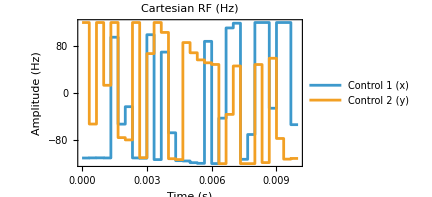
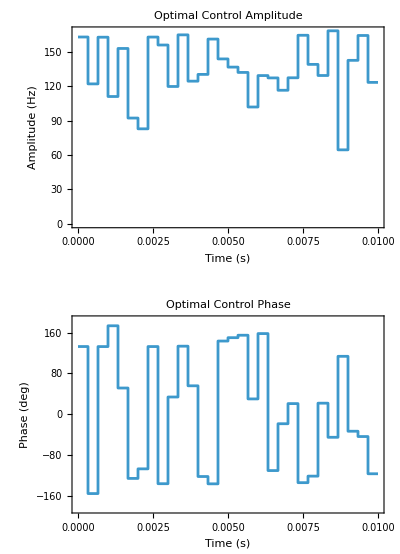
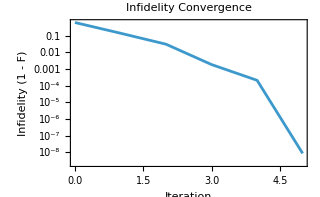
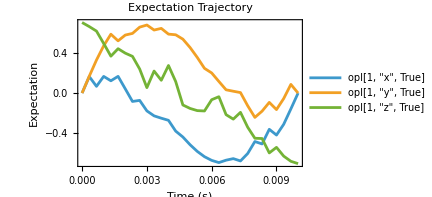
-Graphics- | -Graphics-
-Graphics- | -Graphics-

```mathematica
Grid[{{
  PlotOptimalControlWaveform[resInv, PlotLabel -> "Cartesian RF (Hz)", ImageSize -> 320],
  PlotOptimalControlWaveform[resInv, Method -> "AmplitudePhase", ImageSize -> 320]
}, {
  PlotOptimalControlConvergence[resInv, Method -> "Infidelity", ImageSize -> 320],
  PlotOptimalControlTrajectory[resInv, ks1[[1]], {opI[1, "x"], opI[1, "y"], opI[1, "z"]}, ImageSize -> 320]
}}]
```

## Interactive Exploration

Lab 1A defines clean helper functions runLab1A and renderLab1A driving an interactive DynamicModule. Adjust the resonance offset, pulse duration, slice count, circular RF limit (AmplitudeNormBound), or target mode, then click 'Run GRAPE Optimisation' (executed asynchronously via Method -> "Queued"). Switching the View selector updates plots instantaneously without rerunning GRAPE.

```mathematica
runLab1A[offsetHz_, durMs_, nt_, rfBoundHz_, mode_String, seed_: 11] := Module[
  {b, ks, u90, u180, targ, initOp, obsList, res, sim},
  SetSpinSystem[1];
  b = ZeemanBasis[]; ks = BasisKets[b];
  u90 = MatrixExp[-I (Pi/2.) Normal[MatrixRepresentation[opI[1, "x"], b]]];
  u180 = MatrixExp[-I Pi Normal[MatrixRepresentation[opI[1, "x"], b]]];
  {targ, initOp, obsList} = Switch[mode,
    "State Inversion", {StateTarget[ks[[1]] -> ks[[2]]], opI[1, "z"], {opI[1, "x"], opI[1, "y"], opI[1, "z"]}},
    "Universal pi/2_x", {UnitaryTarget[u90], opI[1, "z"], {opI[1, "x"], opI[1, "y"], opI[1, "z"]}},
    "Universal pi_x", {UnitaryTarget[u180], opI[1, "z"], {opI[1, "x"], opI[1, "y"], opI[1, "z"]}},
    _, {ObservableTarget[opI[1, "z"] -> -opI[1, "y"]], opI[1, "z"], {opI[1, "x"], opI[1, "y"], opI[1, "z"]}}
  ];
  res = GRAPEOptimize[offsetHz opI[1, "z"], {opI[1, "x"], opI[1, "y"]}, targ,
    {N[durMs/1000.], nt}, FrequencyUnits -> "Hz", ControlUnits -> "Hz",
    AmplitudeNormBound -> N[rfBoundHz], TargetFidelity -> 0.9999, MaxIterations -> 120, RandomSeed -> seed];
  sim = VerifyOptimalControlSimulation[res];
  <|"Result" -> res, "Sim" -> sim, "InitOp" -> initOp, "ObsList" -> obsList, "Mode" -> mode|>
];

renderLab1A[data_Association, view_String] := Module[{res = data["Result"], sim = data["Sim"]},
  Column[{
    Panel[Row[{
      "Mode: ", Style[data["Mode"], Bold],
      "   F = ", Style[NumberForm[res["FinalFidelity"], 6], Bold],
      "   Iters = ", res["Iterations"],
      "   Status = ", res["Status"],
      "   SDMatch = ", sim["FidelityMatchQ"]
    }, "  "]],
    Switch[view,
      "Cartesian", PlotOptimalControlWaveform[res, Method -> "Cartesian", ImageSize -> 480],
      "AmplitudePhase", PlotOptimalControlWaveform[res, Method -> "AmplitudePhase", ImageSize -> 480],
      "Infidelity", PlotOptimalControlConvergence[res, Method -> "Infidelity", ImageSize -> 480],
      _, PlotOptimalControlTrajectory[res, data["InitOp"], data["ObsList"], ImageSize -> 480]
    ]
  }]
];
lab1ADefault = runLab1A[50., 10., 30, 120., "Universal pi/2_x", 11];
lab1ADefault["Result"]["FinalFidelity"]
```

SetSpinSystem::set: the spin system has been set to {{1,1/2}}

0.999958

```mathematica
DynamicModule[{offsetHz = 50., durMs = 10., nt = 30, rfHz = 120.,
  mode = "Universal pi/2_x", view = "Cartesian", data = lab1ADefault, running = False},
  Panel[Column[{
    Grid[{
      {"Target Mode", PopupMenu[Dynamic[mode], {"State Inversion", "Universal pi/2_x", "Universal pi_x", "Point-to-Point Iz->-Iy"}]},
      {"Offset (Hz)", Row[{Slider[Dynamic[offsetHz], {-200., 200., 5.}], " ", Dynamic[offsetHz]}]},
      {"Duration (ms)", Row[{Slider[Dynamic[durMs], {2., 20., 0.5}], " ", Dynamic[durMs]}]},
      {"Slices Nt", SetterBar[Dynamic[nt], {10, 20, 30, 50}]},
      {"RF Disk Limit (Hz)", Row[{Slider[Dynamic[rfHz], {40., 250., 5.}], " ", Dynamic[rfHz]}]},
      {"Plot View (Instant)", SetterBar[Dynamic[view], {"Cartesian", "AmplitudePhase", "Infidelity", "Trajectory"}]}
    }, Alignment -> Left],
    Row[{
      Button["Run GRAPE Optimisation", running = True; data = runLab1A[offsetHz, durMs, nt, rfHz, mode]; running = False, Method -> "Queued"],
      " ", Dynamic[If[running, "Optimising...", "Ready"]]
    }],
    Dynamic[renderLab1A[data, view]]
  }]]
]
```

Lab 1B uses an instant Manipulate to inspect forward-only spin evolution (PropagateControls) on the worked inversion pulse without re-optimising: scrub the slice index k from 0 to 30 or shift the test frequency offset away from +50 Hz to observe how sensitively a non-robust single-offset pulse degrades off-resonance.

```mathematica
renderLab1B[res_OptimalControlResult, kSlice_Integer, testOffsetHz_?NumericQ] := Module[
  {b, iX, iY, iZ, nt, dt, uCtrl, uCum, states, traj, curVec, mX, mY, mZ},
  SetSpinSystem[1];
  b = ZeemanBasis[];
  {iX, iY, iZ} = Table[2. Normal[MatrixRepresentation[opI[1, ax], b]], {ax, {"x", "y", "z"}}];
  uCtrl = res["Controls"]; dt = res["TimeSteps"]; nt = Length[dt];
  uCum = FoldList[Dot, IdentityMatrix[2], Table[
    MatrixExp[-I dt[[j]] (2. Pi (testOffsetHz 0.5 iZ + uCtrl[[j, 1]] 0.5 iX + uCtrl[[j, 2]] 0.5 iY))],
    {j, nt}]];
  states = Map[# . (0.5 iZ) . ConjugateTranspose[#] &, uCum];
  traj = Map[{Re[Tr[# . (0.5 iX)]]*2., Re[Tr[# . (0.5 iY)]]*2., Re[Tr[# . (0.5 iZ)]]*2.} &, states];
  curVec = traj[[kSlice + 1]];
  {mX, mY, mZ} = curVec;
  Column[{
    Row[{"Slice k = ", kSlice, "/", nt, "   Test offset = ", testOffsetHz, " Hz   Bloch = ", NumberForm /@ {mX, mY, mZ}}],
    ListLinePlot[Transpose[{Prepend[Accumulate[dt]*1000., 0.], #}] & /@ Transpose[traj],
      PlotLegends -> {"2<Ix>", "2<Iy>", "2<Iz>"}, Frame -> True,
      FrameLabel -> {"Time (ms)", "Bloch Component"}, PlotRange -> {-1.05, 1.05},
      Epilog -> {Dashed, Gray, Line[{{Accumulate[Prepend[dt, 0.]][[kSlice + 1]]*1000., -1.05}, {Accumulate[Prepend[dt, 0.]][[kSlice + 1]]*1000., 1.05}}]},
      ImageSize -> 460]
  }]
];
Manipulate[
  renderLab1B[resInv, kSlice, testOffsetHz],
  {{kSlice, 30, "Slice Index k"}, 0, 30, 1, Appearance -> "Labeled"},
  {{testOffsetHz, 50., "Test Offset (Hz)"}, -150., 150., 5., Appearance -> "Labeled"}
]
```

SetSpinSystem::set: the spin system has been set to {{1,1/2}}

## Suggested Experiments

1. Minimum Pulse Duration: In Lab 1A, lower the duration from 10 ms toward 2 ms at RF limit 120 Hz for Universal pi/2_x versus State Inversion. Where does each hit the quantum speed limit?

2. Discretisation coarseness: Drop Nt from 30 to 10 slices at +150 Hz offset and inspect whether 10 piecewise-constant slices still afford enough degrees of freedom.

3. Amplitude vs Duration trade-off: Reduce RF Disk Limit from 120 Hz to 50 Hz at 10 ms duration and compare Cartesian vs AmplitudePhase waveforms.

4. Bandwidth sensitivity: In Lab 1B, shift Test Offset from +50 Hz to 0 Hz or +150 Hz; observe why a pulse optimised at a single offset fails away from 50 Hz (motivating Notebook 05).

## Summary

We demonstrated single-spin inversion and universal pi/2_x synthesis in Hz units, verified propagator equivalence with SpinDynamica's NPropagationOperator, and contrasted point-to-point state transfer against full unitary gates. Using queued evaluation buttons for GRAPE optimisations paired with instant forward propagation enables rapid interactive exploration without FrontEnd freezes.

Return to 00_OptimalControl_Tutorials_Index.nb or consult the executable CLI fixture (Tutorial01_SingleSpinInversion.wls, Tutorial02_Universal90Rotation.wls) and Manual Ch. 1, 3, 14.